Se quiere ver como es la dinámica de la producción del biodiesel. Gracias a las ecuaciones de Michaelis-Menten se tiene como es las ecuaciones de trabajo.

```mathematica
eq1 = F'[t]== -Subscript[k, 1] Subscript[S, 1][t]*F[t]+Subscript[k, -1] Subscript[FS, 1][t] +SubPlus[a] Subscript[F, e][t]-SubMinus[a] F[t];
eq2 = Subscript[FS, 1]'[t]== Subscript[k, 1] Subscript[S, 1][t]*F[t]-(Subscript[k, 2]+Subscript[k, -1])Subscript[FS, 1][t];
eq3 = Subscript[S, 1]'[t]== -Subscript[k, 1]Subscript[S, 1][t]*F[t]+(Subscript[k, 2]+Subscript[k, -1])Subscript[FS, 1][t];
eq4 = Adh'[t]== Subscript[k, 2] Subscript[FS, 1][t] -Subscript[k, 3]( Subscript[S, 2][t]*Adh[t]) + Subscript[k, -3] Subscript[AdhS, 2][t];
eq5 = Subscript[AdhS, 2]'[t]== Subscript[k, 3] (Subscript[S, 2][t]*Adh[t])-(Subscript[k, 4]+Subscript[k, -3])Subscript[AdhS, 2][t];
eq6 = Subscript[S, 2]'[t]==-Subscript[k, 3](Subscript[S, 2][t]*Adh[t])+(Subscript[k, 4]+Subscript[k, -3])Subscript[AdhS, 2][t];
eq7 = Ak '[t]==Subscript[k, 4] Adh[t];
eq8 = Subscript[F, e]'[t]== -SubPlus[a]Subscript[F, e][t]+SubMinus[a] F[t];

equations1 ={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};
initialConditions1 = {F[0]==10,Subscript[F, e][0]==500,Subscript[S, 1][0]==10,Subscript[S, 2][0]==10,Subscript[FS, 1][0]==0,Subscript[AdhS, 2][0]==0,Adh[0]==0,Ak[0]==0};
```

```mathematica
constants ={Subscript[k, 1]-> 1,Subscript[k, -1]->0.1,Subscript[k, 2]->1,Subscript[k, 3]-> 1,Subscript[k, -3]->0.1,Subscript[k, 4]->0.001,SubMinus[a]->0.1,SubPlus[a]->2};
s=NDSolve[{equations1,initialConditions1}/.constants,{F,Subscript[F, e],Subscript[FS, 1],Subscript[S, 1],Adh,Subscript[AdhS, 2],Subscript[S, 2],Ak},{t,0,1000}]
```

{{F→InterpolatingFunction[…],F_e→InterpolatingFunction[…],FS_1→InterpolatingFunction[…],S_1→InterpolatingFunction[…],Adh→InterpolatingFunction[…],AdhS_2→InterpolatingFunction[…],S_2→InterpolatingFunction[…],Ak→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[{F[t],Subscript[F, e][t],Subscript[FS, 1][t],Subscript[S, 1][t],Adh[t],Subscript[AdhS, 2][t],Subscript[S, 2][t],Ak[t]}/.s],{t,0,1000},PlotRange->{{0,1000},{0,500}},PlotLabels->{"F","F_e","FS_1","S_1","Adh","AdhS_2","S_2","Ak"}]
```

-Graphics-

```mathematica
Plot[Evaluate[{F[t],Subscript[F, e][t],Adh[t],Ak[t]}/.s],{t,0,60},PlotRange->{{0,60},{0,500}},PlotLabels->{"F","F_e","Adh","Ak"}]
```

-Graphics-

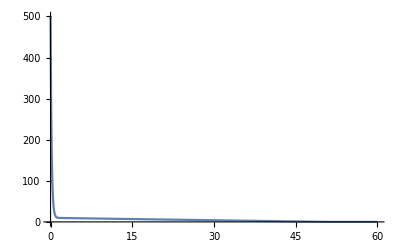

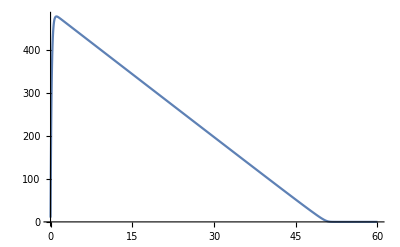

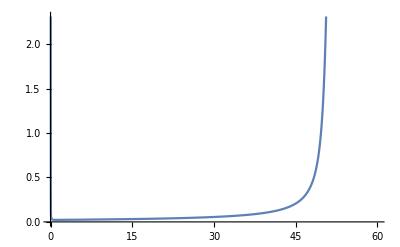

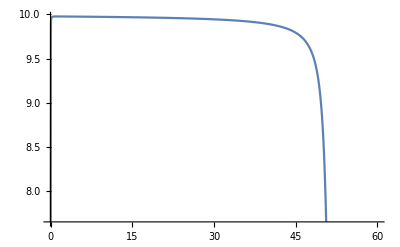

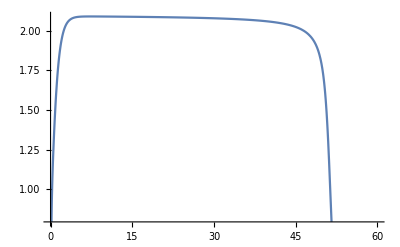

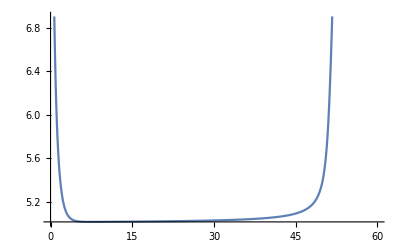

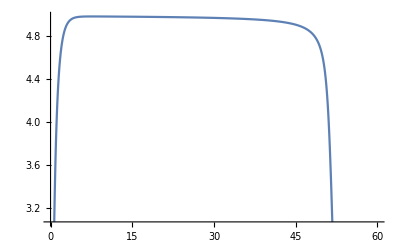

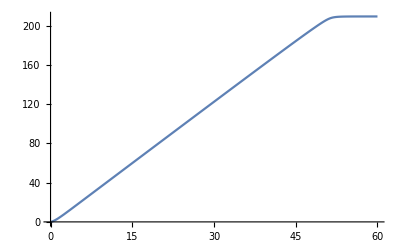

```mathematica
Plot[Evaluate[Subscript[F, e][t]/.s],{t,0,60},PlotLabel->"Fatty outside",PlotRange->{{0,60},{0,500}}]
Plot[Evaluate[F[t]/.s],{t,0,60},PlotLabel->"Fatty inside"]
Plot[Evaluate[Subscript[S, 1][t]/.s],{t,0,60},PlotLabel->"Enzyme 1"]
Plot[Evaluate[Subscript[FS, 1][t]/.s],{t,0,60},PlotLabel->"FE_1Complex"]
Plot[Evaluate[Adh[t]/.s],{t,0,60},PlotLabel->"Fatty inside"]
Plot[Evaluate[Subscript[S, 2][t]/.s],{t,0,60}]
Plot[Evaluate[Subscript[AdhS, 2][t]/.s],{t,0,60}]
Plot[Evaluate[Ak[t]/.s],{t,0,60}]
```